```mathematica
Needs["NDSolve`FEM`"]
```

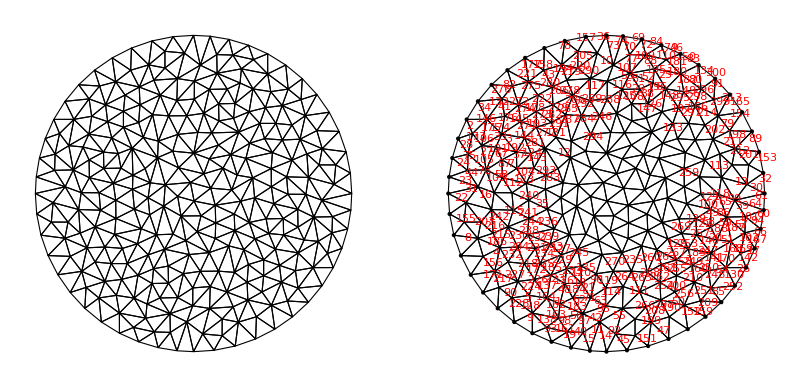

```mathematica
Ω = Disk[{0,0},1];mesh=ToElementMesh[Ω, "MeshOrder"->1];
GraphicsRow[{mesh["Wireframe"],
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]]}]
```

```mathematica
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"][[1,1]];
boundary =Flatten[mesh["BoundaryElements"][[1,1]]];
boundary=DeleteDuplicates[boundary];

json = {"nodes"-> nodes, "elements"-> elements, "dirichletboundary"-> boundary};
```

```mathematica
Export["C:\\Users\\Vasil\\Desktop\\circle_normal_mesh.json",json];
```

```mathematica
locMassMtxInternal[verts_, polys_ ,k_]:= Module[{lM, t},
t =Triangle[{verts⟦polys⟦k,1⟧⟧,verts⟦polys⟦k,2⟧⟧, verts⟦polys⟦k,3⟧⟧ }];
lM =  Area[t]*1/12{{2,1,1},{1,2,1},{1,1,2}};
Return[lM];
];
locStiffnessMtxInternal[verts_, polys_ ,k_]:= Module[{lM, Jac,commonMtx,B, Etriag},
Jac[i_]:= {{verts⟦polys⟦i,2⟧,1⟧-verts⟦polys⟦i,1⟧,1⟧, verts⟦polys⟦i,2⟧,2⟧-verts⟦polys⟦i,1⟧,2⟧},{verts⟦polys⟦i,3⟧,1⟧-verts⟦polys⟦i,1⟧,1⟧,verts⟦polys⟦i,3⟧,2⟧-verts⟦polys⟦i,1⟧,2⟧}} ;

B[i_]:= {{ verts⟦polys⟦i,3⟧,2⟧-verts⟦polys⟦i,1⟧,2⟧,verts⟦polys⟦i,1⟧,2⟧-verts⟦polys⟦i,2⟧,2⟧},{verts⟦polys⟦i,1⟧,1⟧-verts⟦polys⟦i,3⟧,1⟧,verts⟦polys⟦i,2⟧,1⟧-verts⟦polys⟦i,1⟧,1⟧}};

commonMtx = {{-1,1,0},{-1,0,1}};
(*The area of the unit triangle is 1/2!*)
lM =1/(2 Det[Jac[k]])Transpose[commonMtx].Transpose[B[k]].B[k].commonMtx;
Return[lM];
 ];
assembleGlobalMtx[verts_, polys_,locMtxInternal_]:= Module[{globalMtx, n,i,k,m, lM,nullsegment},
n = Length[verts];
globalMtx = Table[0,{i,1,n},{j,1,n}];

For[i =1, i≤ Length[polys], i++,
lM = locMtxInternal[verts, polys, i];
For[k = 1, k ≤ Length[lM], k++,
For[m= 1,m≤ Length[lM], m++,
globalMtx[[polys⟦i, k⟧, polys⟦i,m⟧]] += lM⟦k,m⟧;
]; 
]; 

];
Return[globalMtx];
];
```

```mathematica
lumpMassMatrix[M_]:= DiagonalMatrix[Table[Sum[M⟦i,j⟧,{j,1,Length[M⟦i⟧]}],{i,1,Length[M]}]]
```

```mathematica
M0 = assembleGlobalMtx[nodes, elements,locMassMtxInternal] ;
M1 = assembleGlobalMtx[nodes, elements,locStiffnessMtxInternal ] ;
Mtild = -PseudoInverse[M0].M1;
```

```mathematica
u0[nodes_]:= Table[If[Norm[nodes⟦i⟧,2]≤ 0.5, 100, 0],{i,1,Length[nodes]}]
f0 =Interpolation[Transpose[{nodes,u0[nodes]}],InterpolationOrder->1];
Plot3D[f0[x,y], {x,y}∈Ω]
```

-Graphics3D-

```mathematica
explicitEuler[f_,u0_,t0_,T_,h_]:= Module[{n,t,y,i},
n = Ceiling[(T-t0)/h];
t= Table[t0+i*h,{i,0,n}];
y = Table[u0,{i,0,n}];
Monitor[For[i=1, i≤n, i++ ,
y⟦i+1⟧ = y⟦i⟧ + h*f[t⟦i⟧,y⟦i⟧];
],ProgressIndicator[i/n]];
Return[{t,y}];
];
```

```mathematica
rhs[t_,y_]:= Mtild.y
```

```mathematica
{ts, ys}= explicitEuler[rhs, u0[nodes], 0, 2, 0.00001];
```

```mathematica
ys[[6]]
```

{-0.00532379,-0.00254514,0.00450227,0.0047716,0.00762256,0.00871832,-0.0000114819,0.00467577,0.000773735,-0.00332366,0.00724616,0.000510059,-0.0055249,-0.00216092,0.00428224,0.00466565,0.00754058,0.0086194,-0.0000666854,0.00462095,0.00077534,-0.00332072,0.00723823,0.000534126,-0.0054699,-0.0021555,0.00427444,0.0045267,0.00768989,0.00885561,0.00159827,0.00470938,-0.000401806,-0.00194162,0.0078854,0.00125555,-0.00529436,-0.00254253,0.00448981,0.00462814,0.00770993,0.00887709,0.00160787,0.00471755,-0.000403073,-0.00194433,0.00788809,0.00123891,0.00961533,0.00968101,0.0112653,0.0113701,-0.0164484,-0.0164533,-0.0155695,-0.0155821,0.12394,0.12402,0.126566,0.127545,0.0739285,0.0738904,0.0667824,0.0667485,0.555193,-0.0355774,0.554649,-0.0355766,0.592728,-0.0417899,0.59177,-0.0417685,-0.648461,-0.00797284,-0.648233,-0.00796475,-0.582911,-0.00560017,-0.583492,-0.00559637,96.2545,96.2553,96.1333,96.1463,0.429599,0.429238,0.403035,0.399145,-0.0150812,-0.0143569,-0.249595,-0.246853,-0.548319,0.0956718,-0.548677,0.0956477,-0.61071,0.135527,-0.611329,0.135497,0.00683289,0.00686617,0.00573346,0.00581294,0.057518,0.0108876,-0.00937852,0.0587058,0.0108865,-0.00937771,0.0568583,0.0125394,-0.0133987,0.0577876,0.0125409,-0.0134253,0.0582611,0.0572042,0.058329,0.0573541,0.0657676,0.0496859,0.0657231,0.0504618,-0.0376746,-0.0379976,-0.0335981,-0.0342028,-0.0153007,-0.025457,-0.0154027,-0.024883,-0.014925,-0.0253917,-0.0149917,-0.0245979,-0.00766827,-0.101958,-0.00502202,1.47689,-0.356588,0.954906,98.0882,-0.155383,1.58209,-0.306754,0.199099,99.4743,-0.00761834,-0.102315,-0.00505046,1.47675,-0.356961,0.956793,98.0812,-0.154188,1.60736,-0.313552,0.199961,99.454,-0.0250016,-0.044907,-0.000555823,1.51889,-0.346369,0.795889,99.0685,-0.164715,1.56933,-0.304757,0.204742,99.4948,-0.0246454,-0.0473422,-0.000713823,1.5276,-0.349997,0.812702,99.0356,-0.165047,1.59717,-0.312192,0.21003,99.4949,3.13929,0.564869,97.3099,99.76,2.37013,99.7169,0.066608,-0.00289748,99.8723,3.14118,0.588838,97.1555,99.7529,2.74419,100.258,0.0688705,-0.00255383,99.8673,3.83641,0.567263,97.3059,99.8028,2.37718,99.6991,0.0661209,-0.00268876,3.84054,0.58999,97.1575,99.751,2.74378,100.258,0.068427,-0.00240083,100.139,0.00191326,100.339,100.474,99.925,100.052,0.00173125,100.334,100.52,99.9151,100.075,0.00187063,100.043,0.00171396,99.9277,100.115,99.9558,100.035,99.9862,100.044,100.078,100.343,100.028,99.9022,100.016,100.03,100.017,99.9944,99.995,100.033,99.9323,100.074,100.434,99.903,100.031,-0.101058,-0.101167,-0.111974,-0.112084,-0.00507638,-0.00538907,-0.00501737,-0.00531864,-0.00746109,0.0768466,98.7168,-0.00747879,0.0765725,98.7139,-0.0065635,0.0778977,98.6445,-0.00666251,0.0783634,98.58,100.33,99.9518,100.293,99.9556}

```mathematica
Mtild
```